## SmootheCell-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.0 (10-Nov-2012)) loaded Sun 11 Nov 2012 11:19:12
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

Generate a list of points on a square grid +/- some randomization, and find the Bounded Voronoi Tissue

```mathematica
r:= RandomReal[{-2,2}]; 
v=Partition[Flatten[Table[{x+r, y+r}, {x,0,20,5}, {y,0,20,5}]],2];
w=BoundedCellVoronoi[v];
```

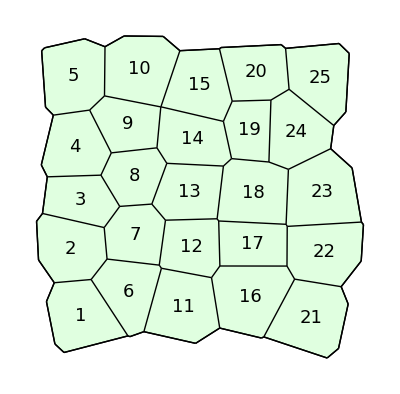

```mathematica
ShowTissue[w, "CellNumbers"-> True, "CellNumberStyle"-> {FontSize-> 18} ]
```

#### Figure out which cells are on top

```mathematica
CT=CellsOnTop[w]
```

{5,10,15,20,25}

#### Pick one of the top cells and smoothe it

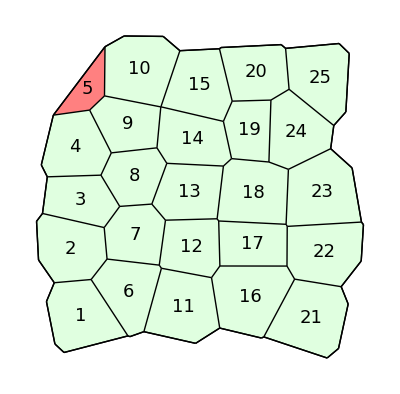

```mathematica
c=CT[[1]];
x=SmootheCell[w,c];
ShowTissueCells[x,{c},Pink,  "CellNumbers"-> True,"CellNumberStyle"-> {FontSize-> 18}]
```

#### Smoothe all the cells on top

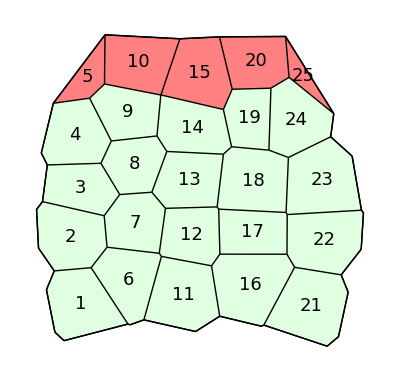

```mathematica
x=SmootheCells[w, CT];
ShowTissueCells[x,CT,Pink,  "CellNumbers"-> True,"CellNumberStyle"-> {FontSize-> 18}]
```

#### Smoothe all the cells on the boundary in two different ways

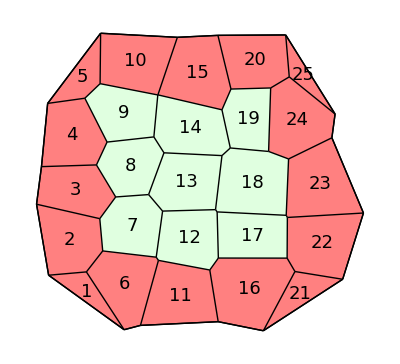

```mathematica
BC = CellsOnBoundary[w];
x=SmootheCells[w,BC];
ShowTissueCells[x, BC, Pink, "CellNumbers"-> True, "CellNumberStyle"-> {FontSize-> 18}]
```

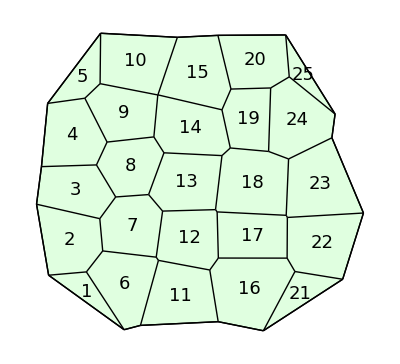

```mathematica
x=SmootheCells[w];
ShowTissue[x, "CellNumbers"-> True, "CellNumberStyle"-> {FontSize-> 18}]
```